```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions`
```

```mathematica
tol=10^(-6);
spPar[c_]:=Abs[c[[3]]]*{Cos[u],Sin[u]}+c[[1;;2]]
coneS[arc_,pt_]:=v*Join[arc,{0}]+(1-v)*pt
```

```mathematica
cpts=Table[{6*(i-1),0,0}+Join[{RandomReal[{-4,4}]},{RandomReal[{-4,4}]},{RandomReal[{0,5}]}],{i,1,6}];
c=BCurve[cpts,t];
dn=Simplify@MInnProd[D[c,t],D[c,t]];
While[Length@Solve[dn==0&&0≤t≤1,t,Reals]>0,(
cpts=Table[{4*(i-1),0,0}+Join[{RandomReal[{-6,6}]},{RandomReal[{-6,6}]},{RandomReal[{0,10}]}],{i,1,6}];
c=BCurve[cpts,t];
dn=Simplify@MInnProd[D[c,t],D[c,t]];
)]
```

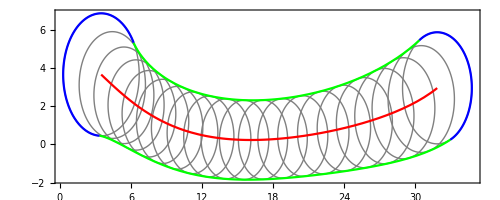

```mathematica
envs=Env[c,t,10^(-6)];
ecaps=EndCap[c,t,tol]/.{t->s};
ts=Table[i,{i,0,1,1/20}];

Show[
Table[ParametricPlot[spPar[c/.{t->T0}],{u,0,2Pi},PlotStyle->{Thin,Gray}],{T0,ts}],
ParametricPlot[c[[1;;2]],{t,0,1},PlotStyle->Red],
ParametricPlot[envs,{t,0,1},PlotStyle->Green],
ParametricPlot[ecaps,{s,0,1},PlotStyle->Blue],
PlotRange->All,Frame->True,Axes->False,LabelStyle->Medium,AspectRatio->Automatic
]
```

```mathematica
Show[
ParametricPlot3D[c,{t,0,1},PlotStyle->{Thick,Red}],
ParametricPlot3D[Join[c[[1;;2]],{0}],{t,0,1},PlotStyle->{Thick,Red}],
ParametricPlot3D[Join[envs[[1]],{0}],{t,0,1},PlotStyle->Green],
ParametricPlot3D[Join[envs[[2]],{0}],{t,0,1},PlotStyle->Green],
ParametricPlot3D[Join[ecaps[[1]],{0}],{s,0,1},PlotStyle->Blue],
ParametricPlot3D[Join[ecaps[[2]],{0}],{s,0,1},PlotStyle->Blue],
ParametricPlot3D[coneS[ecaps[[1]],c/.{t->0}],{s,0,1},{v,0,1},Mesh->None,PlotStyle->{Lighter@Blue,Opacity[0.4]}],
ParametricPlot3D[coneS[ecaps[[2]],c/.{t->1}],{s,0,1},{v,0,1},Mesh->None,PlotStyle->{Lighter@Blue,Opacity[0.4]}],ParametricPlot3D[(1-v)*c+v*Join[envs[[1]],{0}],{t,0,1},{v,0,1},Mesh->None,PlotStyle->{Lighter@Green,Opacity[0.5]}],
ParametricPlot3D[(1-v)*c+v*Join[envs[[2]],{0}],{t,0,1},{v,0,1},Mesh->None,PlotStyle->{Lighter@Green,Opacity[0.5]}],
PlotRange->All,LabelStyle->Medium,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
NN=6;
cols={RGBColor[0.77, 0.07, 0.9400000000000001],RGBColor[0.901627, 0.5398719999999999, 0.208366]};
```

```mathematica
(*DAI*)
ts=Table[i,{i,0,1,1/NN}];
ints=Table[ts[[2i-1;;2i+1]],{i,1,(Length@ts-1)/2}];
mpts=Table[Table[c/.{t->ints[[i,j]]},{j,1,Length@ints[[i]]}],{i,1,Length@ints}];
mArcs=Table[MinkArcParam[mpts[[i]],t,tol],{i,1,Length@mpts}];
aEnvs=Table[Env[mArcs[[i]],t,tol],{i,1,Length@mArcs}];
ecp=Table[EndCap[mArcs[[i]],t,tol],{i,1,Length@aEnvs}];
```

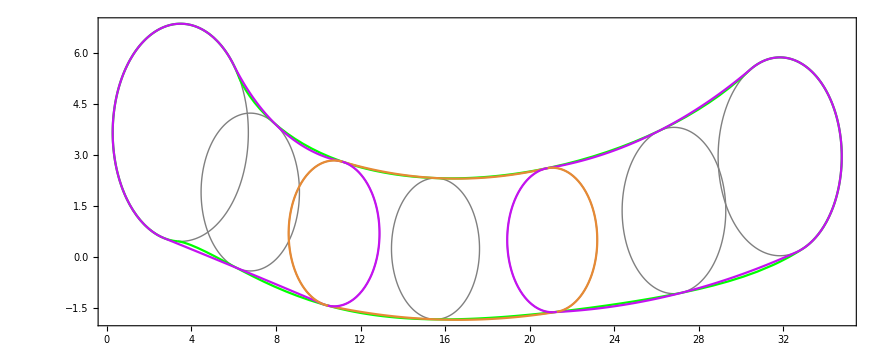

```mathematica
shDAI=Show[
Table[ParametricPlot[spPar[c/.{t->T0}],{u,0,2Pi},PlotStyle->{Thin,Gray}],{T0,ts}],
ParametricPlot[envs,{t,0,1},PlotStyle->Green],
ParametricPlot[ecaps,{s,0,1},PlotStyle->Green],
ParametricPlot[aEnvs,{t,0,1},PlotStyle->{cols[[1]],cols[[2]]}],
Table[ParametricPlot[ecp[[i]],{t,0,1},PlotStyle->cols[[Mod[i,2,1]]]],{i,1,Length@ecp}],
PlotRange->All,Frame->True,Axes->False,LabelStyle->Medium,AspectRatio->Automatic]
```

```mathematica
(*DBI*)
ts=Table[i,{i,0,1,1/NN}];
ints=Table[ts[[i;;i+1]],{i,1,Length@ts-1}];
mpts=Table[Table[c/.{t->ints[[i,j]]},{j,1,Length@ints[[i]]}],{i,1,Length@ints}];
mtgs=Table[Table[Normalize[D[c,t]/.{t->ints[[i,j]]}],{j,1,Length@ints[[i]]}],{i,1,Length@ints}];
mbiarcs=Table[MinkBiarc[mpts[[i,1]],mtgs[[i,1]],mpts[[i,2]],mtgs[[i,2]],t,tol],{i,1,Length@ints}];
mbEnv=Table[Transpose[{Env[mbiarcs[[i,1]],t,tol],Env[mbiarcs[[i,2]],t,tol]}],{i,1,Length@ints}];
```

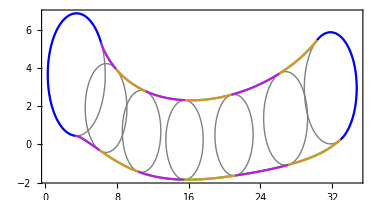

```mathematica
shDBI=Show[
Table[ParametricPlot[spPar[c/.{t->T0}],{u,0,2Pi},PlotStyle->{Thin,Gray}],{T0,ts}],
ParametricPlot[envs,{t,0,1},PlotStyle->Green],
ParametricPlot[ecaps,{s,0,1},PlotStyle->Blue],
Table[ParametricPlot[mbEnv[[i,All]],{t,0,1},PlotStyle->cols[[Mod[i,2,1]]]],{i,1,NN}],
PlotRange->All,Frame->True,Axes->False,LabelStyle->Medium,AspectRatio->Automatic
]
```

```mathematica
(*IAI*)
ts=Table[i,{i,0,1,1/NN}];
ints=Table[ts[[2i-1;;2i+1]],{i,1,(Length@ts-1)/2}];
epts=Table[Table[Table[envs[[k]]/.{t->ints[[i,j]]},{j,1,Length@ints[[i]]}],{i,1,Length@ints}],{k,1,Length@envs}];
eArcs=Table[Table[ArcFrom3Pts[epts[[k,i,1]],epts[[k,i,2]],epts[[k,i,3]],t],{i,1,Length@epts[[k]]}],{k,1,Length@epts}];
eArcs=Transpose[eArcs];
```

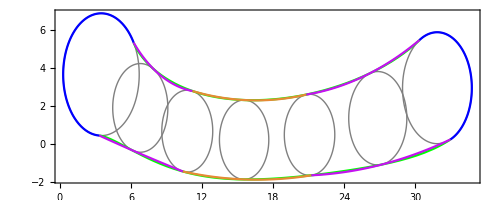

```mathematica
shIAI=Show[
Table[ParametricPlot[spPar[c/.{t->T0}],{u,0,2Pi},PlotStyle->{Thin,Gray}],{T0,ts}],
ParametricPlot[envs,{t,0,1},PlotStyle->Green],
ParametricPlot[ecaps,{s,0,1},PlotStyle->Blue],
Table[ParametricPlot[eArcs[[i]],{t,0,1},PlotStyle->cols[[Mod[i,2,1]]]],{i,1,Length@eArcs}],
PlotRange->All,Frame->True,Axes->False,LabelStyle->Medium,AspectRatio->Automatic]
```

```mathematica
(*IBI*)
ts=Table[i,{i,0,1,1/NN}];
ints=Table[ts[[i;;i+1]],{i,1,Length@ts-1}];
epts=Table[Table[Table[envs[[k]]/.{t->ints[[j,i]]},{i,1,Length@ints[[j]]}],{k,1,Length@envs}],{j,1,Length@ints}];
etgs=Table[Table[Table[Normalize[D[envs[[k]],t]/.{t->ints[[j,i]]}],{i,1,Length@ints[[j]]}],{k,1,Length@envs}],{j,1,Length@ints}];
eBiArcs=Table[Table[BiArc[epts[[j,k,1]],etgs[[j,k,1]],epts[[j,k,2]],etgs[[j,k,2]],t,tol],{k,1,Length@epts[[j]]}][[All,2]],{j,1,Length@ints}];
```

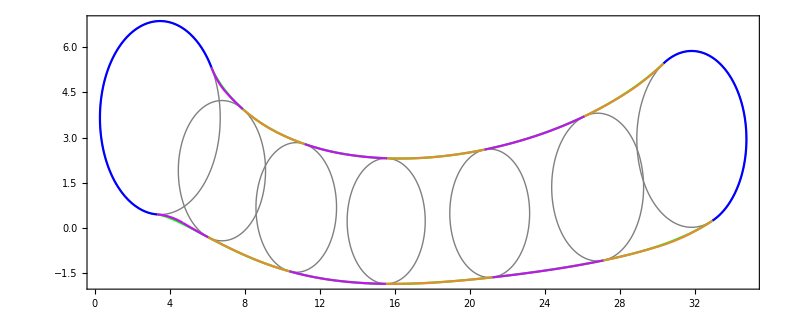

```mathematica
shIBI=Show[
Table[ParametricPlot[spPar[c/.{t->T0}],{u,0,2Pi},PlotStyle->{Thin,Gray}],{T0,ts}],
ParametricPlot[envs,{t,0,1},PlotStyle->Green],
ParametricPlot[ecaps,{s,0,1},PlotStyle->Blue],
Table[ParametricPlot[eBiArcs[[i]],{t,0,1},PlotStyle->cols[[Mod[i,2,1]]]],{i,1,NN}],
PlotRange->All,Frame->True,Axes->False,LabelStyle->Medium,AspectRatio->Automatic]
```

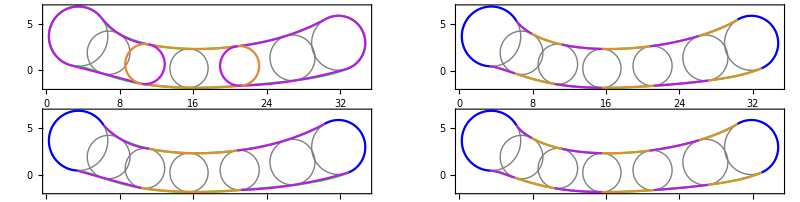

```mathematica
GraphicsGrid[{{shDAI,shDBI},{shIAI,shIBI}}]
```